## Análisis de Algoritmos

## Enfoque Experimental

```mathematica
(* Se utiliza del paquete VilCretas, PruebaADA2 y PruebaADA3 *)
<<VilCretas`
```

```mathematica
(*Por Recursividad: (de pila)*)
```

```mathematica
s1[n_]:= If[n==5, -1/3,s1[n-1]+(-1)^(n-2)/(3(n-4))]
```

```mathematica
(*Si fuera de cola: *)
```

```mathematica
(* Iterativamente: *)
```

```mathematica
s2[n_]:=Module[{suma=0,i},For[i=2,i<=n-3,suma=suma+(-1)^(i+1)/(3(i-1)); i++];suma]
```

```mathematica
(*Con Sum: *)
```

```mathematica
s3[n_]:=Sum[(-1)^(i+1)/(3(i-1)),{i,2,n-3}]
```

```mathematica
Table[s1[j]==s2[j]==s3[j],{j,5,20}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
(* Cuál es el mas eficiente? PruebaADA3, espera 3 funciones *)
```

```mathematica
PruebaADA3[{s1,s2,s3},1000,5]
```

El primer y segundo algoritmo fueron mejores: 18

El primer y tercer algoritmo fueron mejores: 23

El segundo y tercer algoritmo fueron mejores: 32

Se comportaron igual: 923

```mathematica
(* Comparando los últimos 2: *)
```

```mathematica
PruebaADA2[{s2,s3},1500,5]
```

El primer algoritmo fue mejor: 29

El segundo algoritmo fue mejor: 50

Se comportaron igual: 1417

```mathematica
(* Este comando puede recibir cualquier cantidad de funciones *)
PruebaADAGrafica[{s1,s2,s3},25,5]
(* Aumentar el rango: PruebaADAGrafica[{s1,s2,s3},500, 25,5] *)
```

-Graphics-

```mathematica
(* ----------------------------------------------------------------------- *)
```

```mathematica
CalculaProducto[10,code->True]
CalculaOtroProducto[10,code->True]
```

{27,CalculaProducto[n_]:=Module[{p=1},While[p≤n,p=p*3];Return[p]]}

{27,CalculaOtroProducto[n_]:=Module[{p=1},For[i=1,i≤n,While[p≤i,p=p*3];i++];Return[p]]}

```mathematica
Table[CalculaProducto[j]==CalculaOtroProducto[j],{j,1,30}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
(*Solo viéndolos, se puede deducir que el que va a ser más rápido es el primero, porque reitera menos veces, verificar con PrueabaADA2 : *)
```

```mathematica
PruebaADA2[{CalculaProducto,CalculaOtroProducto},5000,1]
```

El primer algoritmo fue mejor: 227

El segundo algoritmo fue mejor: 3

Se comportaron igual: 4770

```mathematica
PruebaADAGrafica[{CalculaProducto,CalculaOtroProducto},25,1]
```

-Graphics-

```mathematica
(* ------------------------------------------------------------------- *)
```

```mathematica
divisores[n_,Cont_:1,Lista_:{}]:=Module[{L=Lista},If[Cont≤n,If[Mod[n,Cont]==0,L=Append[L,Cont]];divisores[n,Cont+1,L],Lista]]
```

```mathematica
(* Esta llega hasta n/2, por lo que se puede deducir que va ser más eficiente*)
```

```mathematica
Otrodivisores[n_,Cont_:1,Lista_:{}]:=Module[{L=Lista},If[Cont≤n/2,If[Mod[n,Cont]==0,L=Append[L,Cont]];Otrodivisores[n,Cont+1,L],Append[Lista,n]]]
```

```mathematica
PruebaADA2[{divisores,Otrodivisores},500,1]
```

El primer algoritmo fue mejor: 1

El segundo algoritmo fue mejor: 9

Se comportaron igual: 490

```mathematica
(* -------------------------------------------------------------------- *)
```

```mathematica
PruebaADA2[{Factoriales, FactorialesCola},1000,1]
```

El primer algoritmo fue mejor: 40

El segundo algoritmo fue mejor: 51

Se comportaron igual: 909

```mathematica
PruebaADAGrafica[{Factoriales, FactorialesCola},400,1,20]
```

-Graphics-

```mathematica
(* Algoritrmos de ordenamiento, comparación: *)
```

```mathematica
Burbuja[{9,37,19,17}]
```

{9,17,19,37}

```mathematica
Insercion[{9,37,19,17}]
```

{9,17,19,37}

```mathematica
PruebaADA2[{Burbuja,Insercion},200,1,1,lista-> True]
```

El primer algoritmo fue mejor: 21

El segundo algoritmo fue mejor: 62

Se comportaron igual: 117

```mathematica
PruebaADAGrafica[{Burbuja, Insercion},400,1,20,lista->True]
```

-Graphics-

## Enfoque Teórico

```mathematica
(* Ejemplo: *)
```

```mathematica
CDFGraficaNOG[1500]
```

```mathematica
(* Ln[n] y Ln[Ln[n]] son más adecuados porque están por debajo de la funcion identidad: n *)
(* No crecen tan rápido como la hace n *)
(* De los peores órdenes asintóticos que se puede tener es el exponencial, le sigue es el polinomial, el n^2 es mejor que n^3*)
(* Orden de peor a mejor: 2^n , n^3, n^2, nln(n), n , ln(n) y ln(ln(n)) *)
```

```mathematica
(* Fórmula, o Teorema del O grande: *)
```

```mathematica
(* f(n) = O g(n) < = > |f(n)| <= c |g(n)| *)
```

```mathematica
(* Cambiar cada sumando por el mayor, en este caso, el mayor es n^3 por lo que se cambia todo por n^3 *)
```

```mathematica
(* n^3 + n^3 + n^3 + 2 n^3 <= 5 n^3  *)
(* => | n^3 + n^3 + n^3 + 2 n^3 | <= 5 n^3 *)
(* n^3 + n^2 + n + 2 = O(n^3)*)
```

```mathematica
CDFGraficaNA[{n^3+n^2+n+2,n^3},0.1,10,1000]
```

FunctionDomain::ivar: 0.000161284 is not a valid variable.

FunctionDomain::ivar: 0.0613837 is not a valid variable.

FunctionDomain::ivar: 0.122606 is not a valid variable.

General::stop: Further output of FunctionDomain::ivar will be suppressed during this calculation.

FunctionDomain::ivar: 0.000161284 is not a valid variable.

FunctionDomain::ivar: 0.0613837 is not a valid variable.

FunctionDomain::ivar: 0.122606 is not a valid variable.

General::stop: Further output of FunctionDomain::ivar
     will be suppressed during this calculation.

FunctionDomain::ivar: 0.000161284 is not a valid variable.

FunctionDomain::ivar: 0.0613837 is not a valid variable.

FunctionDomain::ivar: 0.122606 is not a valid variable.

General::stop: Further output of FunctionDomain::ivar
     will be suppressed during this calculation.

```mathematica
(* El comando recibe el polinomio, el O grande, el valor min, el valor max de c y el valor max de Y y x *)
```

```mathematica
(* A partir de 5, o sea la constante real positiva, se cumple que g está por encima de la identidad o f, el valor de la constante real positiva, no es único *)
```

## Teorema que generaliza polinomios cuando el mayor es j siendo un número N

```mathematica
(* -------------------------------------------------------------------------------------------------- *)
```

```mathematica
(* El mayor seria n^j *)
```

```mathematica
(* Recordar que la notación asintótica se debe cumplir a partir de alguna constante real positiva, y no siempre *)
```

```mathematica
(* Este comando se usa cuando hay j, recibe lo mismo que CDFGraficaNA, la diferencia es que este al final se le agrega el valor max que quiero que tome j *)
```

```mathematica
(* Se puede ver que para c=1, para cualquier valor de j, se va a cumplir la notación asintótica *)
```

```mathematica
CDFGraficaNAP[{Sum[i^j,{i,1,n}],n^(j+1)},0.01,10,1000,10]
```

```mathematica
(*-----------------------------------------------------------------------------------*)
```

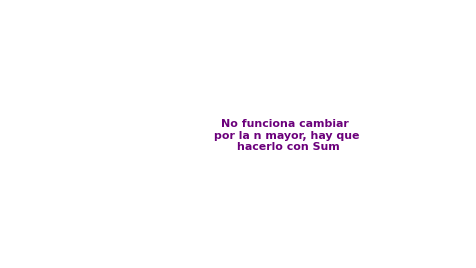
```mathematica
-Graphics--Graphics-
```

```mathematica
(* Siempre intentar probar cambiar el sumando por el n mayor primero *)
Sum[2^j,{j,1,n}]
```

2 (-1+2^n)

```mathematica
(*-------------------------------------------------------------------------------------*)
```

```mathematica
CDFGraficaNA[{Log[n!],n Log[n]},0.01,10,1000]
```

FunctionDomain::ivar: 0.000161284 is not a valid variable.

FunctionDomain::ivar: 0.0613837 is not a valid variable.

FunctionDomain::ivar: 0.122606 is not a valid variable.

General::stop: Further output of FunctionDomain::ivar
     will be suppressed during this calculation.

FunctionDomain::ivar: 0.000161284 is not a valid variable.

FunctionDomain::ivar: 0.0613837 is not a valid variable.

FunctionDomain::ivar: 0.122606 is not a valid variable.

General::stop: Further output of FunctionDomain::ivar
     will be suppressed during this calculation.

## Enfoque Teórico Propiedades

## Propiedades:

## 1) Cualquier número real es O grande de 1:

## 2) Propiedad Reflexiva:

## 3) Propiedad del limite:

```mathematica
(* Ejemplo: *)
```

```mathematica
(* No se puede usar la defincion de cambiar por el n mayor, no es una sumatoria *)
```

```mathematica
Limit[(((n+1)(4n+1))/(7n+1))/n,n->Infinity]
```

4/7

```mathematica
(* **** Si el limite da infinito o negativo, no se puede interpretar que es un O grande **** *)
```

```mathematica
(* Queda demostrado que n si corresponde al O grande de esa funcion, porque da un num *)
(*-----------------------------------------------------------------------------*)
```

## 4) Propiedad de la multiplicación y suma:

```mathematica
(*------------------------------------------------------------------------------------------*)
```

```mathematica
(* No se puede usar la definición porque 2^n no es una sumatoria *)
Limit[2^n/(n!),n->Infinity]
```

0

```mathematica
(* ---------------------------------------------------------------------------*)
```

```mathematica
Limit[(n!)/n^n,n->Infinity]
```

0

```mathematica
(* Se puede hacer tambien por definicion:  *)
```

```mathematica
(*--------------------------------------------------------------------------*)
```

```mathematica
(* Haciendo uso de la propiedad 4*)
```

```mathematica
(*    n! = O(n^n)  *)
```

```mathematica
(*En ln(n^2+5) para calcular el O grande, se quitan todas las constantes => ln n^2 => ln 2n => O(ln n)*)
(* Como da 2 se confirma que sí corresponde al O grande el ln n *)
```

```mathematica
(* Toda la solucion : *)
```

```mathematica
(* Para probar cual de las n es mayor, si se usa Limit, poniendo el que se cree que es mayor abajo, deberia dar 0 o un n real postivo, sino, da infinito *)
```

```mathematica
(* = O(n+3)  *)
```

```mathematica
(* 2) *)
```

```mathematica
(* Por propiedad de la suma: *)
```

```mathematica
(* O grande de lo primero:  *)
```

```mathematica
(* Probando con Limit que n^3 es mayor a n ln n *)
Limit[(n Log n)/n^3,n->Infinity]
```

0

```mathematica
-Graphics-=-Graphics-
```

```mathematica
(* Entre los ultimos dos, n^7 y n^2 ln n el mayor es n^7 *)
```

```mathematica
(*-----------------------------------------------------------------------*)
```

```mathematica
(*En este caso, el peor caso va ser cuando la lista este mas bien ordenada descendentemente *)
```

```mathematica
RR[{1,n-1},{0},n]
```

1/2 (-1+n) n

```mathematica
(* Como n^2 esta arriba que la funcion n en la grafica, no es tan bueno para ordenar eficientemente *)
CDFGraficaNOG[1500]
```

```mathematica
(*-------------------------------------------------------------------------------------------------*)
```

```mathematica
Factoriales[5,code->True,steps->True]
```

{120,Factoriales[n_]:=If[Or[n==0, n==1], Return[1], n*Factoriales[n-1]]}

Factoriales[5] = 5 * Factoriales[4] = 120

Factoriales[4] = 4 * Factoriales[3] = 24

Factoriales[3] = 3 * Factoriales[2] = 6

Factoriales[2] = 2 * Factoriales[1] = 2

Factoriales[1] = 1

120

```mathematica
(* Usando la propiedad que cualquier c = O(1)*)
```

```mathematica
(**********************************************************************************)
```

```mathematica
(* Son dos ciclos For, por lo que se llega hasta n^2 *)
```

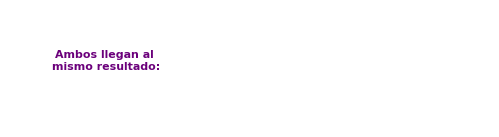
```mathematica
-Graphics--Graphics-
```

```mathematica
(* CUANDO QUIERO VER LA CANT DE VECES QUE CORRE DOS CICLOS ANINADOS, SE MULTIPLICA NO SE SUMA *)
```

```mathematica
CDFGraficaNOG[1500]
```

```mathematica
(*No es apropiado porque n^2 está por encima de la identidad *)
```

```mathematica
(*********************************************************************************************)
```

```mathematica
(*  Por ser un ciclo whie, no es tan fácil ver cuántas veces itera, por lo que se
usa una relación de recurrencia para saber cuánto tiempo dura *)
```

```mathematica
RR[{3},{1},k,inicio->0]
```

3^k

```mathematica
(* Para encontrar quién es k, se niega la condición de entrada del ciclo o sea p <= n *)
(* En este caso, quedaría pk > n *)
```

```mathematica
(* ln -> logaritmo natural, se despeja la desigualdad *)
(* Lo que quiere decir es que k es un entero mayor que (ln n)/ln3  *)
(* Para averiguar quién es k, se debe de sacar el entero superior o parte entero superior a (ln n)/ln3 *)
```

```mathematica
(* 1) entera inferior, redondea hacia abajo -> 5.5 = 5
2) entera superior redondea hacia arriba -> 5.5 = 6 *)
```

```mathematica
(* el + a , permite redondear hacia arriba *)
```

```mathematica
(* Entonces, se intuye que k = eliminar todo lo constante de la respuesta, o sea, ln 3 y a*)
```

```mathematica
(* Para verificar: *)
```

```mathematica
(* Si el resultado da un numero real o 0, se puede afirmar que el O grande propuesto estaba correcto  *)
```

```mathematica
(* Como se puede ver, ln n está por debajo de la función n, por lo que en números muy grandes no va a tardar mucho *)
```

```mathematica
(**************************************************************************)
```

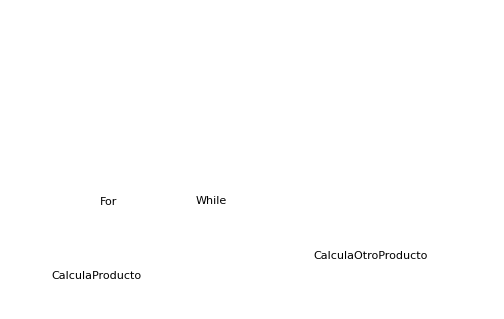
```mathematica
-Graphics--Graphics-
```

```mathematica
(* Se asume que i = n en el while porque se está pensando en el peor escenario, hasta dónde llegarían las iteraciones del while? Hasta n *)
```

```mathematica
(* Es mejor CalculaProducto, porque si se ven en la gráfica, n*ln n está por encima de la función y de ln n *)
```

```mathematica
(**********************************************************************************************)
```

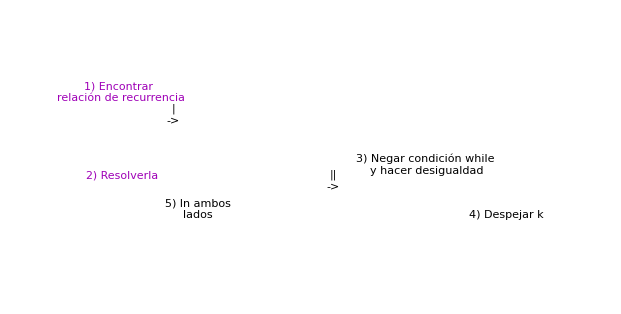
```mathematica
-Graphics--Graphics-
```

```mathematica
(* Respuesta: k = (2 ln)/(ln 2) + a, a E R, O(ln) , porque se quita todo lo que es constante y queda ln *)
(* Verificar: *)
Limit[((2Log[n])/Log[2]+a)/Log[n],n->Infinity]
```

2/Log[2]

```mathematica
(*****************************************************************************************************)
```

```mathematica
(*Para saber cuánto itera el For: *)
```

```mathematica
(* y-x+1 = n+3 -0+1 *)
(* X es 0 porque i = 0*y y es n + 3 porque i <= n+3 *)
```

```mathematica
-Graphics--Graphics-
```

```mathematica
(* 1) Analizar cuál es la peor situacion del For, en qué valor haría más iteracionnes, luego sacar el O grande del For *)
(* 2) Plantear una relación de recurrencia para While *)
(* 3) Resolverla con RR *)
(* 4) Analizar cuál es la peor situacion del while, en qué valor haría más iteraciones *)
(* 5) Plantear una inecuacion o desigualdad negando la entrada del While y resolverla *)
(* 6) Ver el resultado de la inecuacion y intuir cuál sería el O grande *)
(* 7) Verificar con el Limit que ese sí es el O grande *)
```

```mathematica
(* Metodo Preciso, especialmente cuando hay thetas *)
```

```mathematica
(************************************************************************************************)
```

```mathematica
(* Verificando que ese sí es el O grande: *)
```

## Otras Notaciones Asintóticas

```mathematica
(* Omega: busca más bien una cota inferior, para analizar algoritmos en la mejor situacion *)
(* Theta: la función es simultáneamente O grande y Omega *)
```

```mathematica
(* ----------------------------------------------------------------------------- *)
```

```mathematica
(* --------------------------------------------------------------------------------- *)
```

```mathematica
(* Recordar que el Omega busca una cota inferior, para analizar en la mejor situación *)

(* 1) Se empieza desde el entero superior de ln n/2 porque es inferior a la suma entera, o sea n! y así también,se elimina de la suma la mitad de los sumandos y así obtenemos una cota inferior *)

(* 2) Cambiar los sumandos por los más pequeños, o sea cambiarlos por ln n/2 *)

(* 3) La suma de ln n/2 + .... + ln n/2 corresponde a (n+1)/2 ln n/2   *)

(* 4) Reemplaar o "sustituir" n+1/2 por n/2 y la cuota superior de n/2 por n/2,
esto se puede hacer porque al ser una desigualdad o inecuación, 
n/2 es menor que n+1/2 y n/2 es menor que la cuota superior de n/2 *)

(* 5) Si se logra sacar ese 2 del ln se podría llegar a la respuesta de la demostración, pero no no hay propiedades de log que permitan hacer eso *)
(* Así que se va a asumir que es cierto y se va a evaluar en qué casos se cumple: *)
```

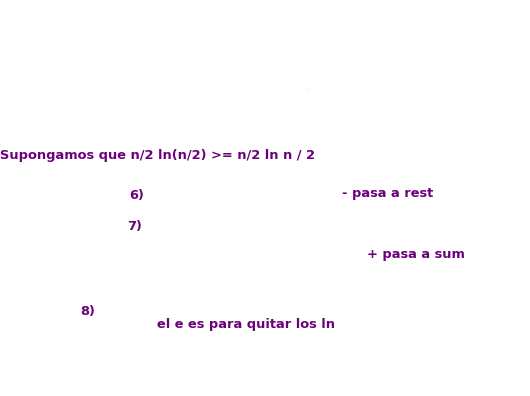
```mathematica
-Graphics--Graphics-
```

```mathematica
(* 6) Se cancelan considerando que n es un num natural *)
(* 7) Se sigue resolviendo la inequación, el ln n/2 pasa a ln n - ln 2 por propiedades de log *)
(* 8) Se encontró entonces que el omega se cumple para los nums naturales a partir de 4 *)
```

```mathematica
CDFGraficaNA[{Log[n!],n Log[n]},0.01,10,1000]
```

FunctionDomain::ivar: 0.000161284 is not a valid variable.

FunctionDomain::ivar: 0.0613837 is not a valid variable.

FunctionDomain::ivar: 0.122606 is not a valid variable.

General::stop: Further output of FunctionDomain::ivar
     will be suppressed during this calculation.

FunctionDomain::ivar: 0.000161284 is not a valid variable.

FunctionDomain::ivar: 0.0613837 is not a valid variable.

FunctionDomain::ivar: 0.122606 is not a valid variable.

General::stop: Further output of FunctionDomain::ivar
     will be suppressed during this calculation.

```mathematica
(*Si se mueve la barra de la c, se puede apreciar que la linea de color naranja puede estar arriba o abajo de la linea celeste *)
(* O sea se presenta una theta *)
```

```mathematica
(*  -------------------------- Propiedades del Theta --------------------------- *)
```

```mathematica
(*A diferencia del O grande: *)
```

```mathematica
(* c tiene que ser positivo *)
(* j tiene que ser positivo *)
```

```mathematica
(* ------------------------------------------------------------------------ *)
```

```mathematica
-Graphics--Graphics-
```

```mathematica
Limit[Log[n!]/(n Log[n]),n->Infinity]
```

1

```mathematica
(* ------------------------------------------------------------------------ *)
```

```mathematica
(*----------------------------------------------------------------------------------*)
```

```mathematica
(* Cuando es theta hay que ser precisos y ver todas las iteraciones del For manualmente, hay que averigiar el num exacto de las asignaciones simples *)
(* TENER CUIDADO CON CICLOS ANINADOS DE FOR O WHILE EN THETA *)
```

```mathematica
(*----------------------------------------------------------------------------------------------*)
(* Si el metodo tiene SOLO un ciclo se resuelve como si fuera un O grande: *)
```

```mathematica
(* Verificación: *)
```

```mathematica
(*Este comando sire para verificar y da el análisis de qué es la notación: *)
```

```mathematica
CompLimit[{Log[n]/Log[7]+a, Log[n]}]
```

1/Log[7]→ (a Log[7]+Log[n])/Log[7]=Θ(Log[n]), Notación theta

```mathematica
(*Si se pone una n^j se puede mover el deslizador y ver si es siempre omega, o grande, etc *)
(* Si se usa jvalor se puede dar mas o menos valores para la barra*)
```

```mathematica
CompLimit[{Log[n]/Log[7]+a,Log[n^j]}]
```

```mathematica
(*-------------------------------------------------------------------------------------------------*)
```

```mathematica
CompLimit[{n^10/(n+1),n^(j+1)}]
```

```mathematica
(*-----------------------------------------------------------------------------------------------------*)
```

```mathematica
(* ********** Floor: parte entera, o sea hay que hacer un O grande *************** *)
(* 1) El num adentro de |_| siempre va a ser más grande *)
(* El For llega hasta n-1 porque se le suma a n-2, 1 porque está empezando en 0 *)
```

```mathematica
-Graphics--Graphics-
```

```mathematica
(*-------------------------------------------------------------------------------------------*)
```

```mathematica
RR[{1,2},{1},k,inicio->0]
```

1+2 k

```mathematica
(*-------------------------------------------------------------------*)
```

```mathematica
(* Como se quiere encontrar una notación theta, se debe de contar con exactitud cuántas veces se hace la asignación del algoritmo, en este caso, p = p*2 *)
```

```mathematica
(*-------------------------------------------------------------------*)
```

```mathematica
Table[cont=0;For[i=1,i<=2k-1,cont=cont+1;i=i+2];cont,{k,1,30}]
FindSequenceFunction[%,n]
```